### No delay Loop

```mathematica
NoDelayLoop:=(For[


Array[AlleleFreqA,Nloci];
Do[AlleleFreqA[i]={},{i,1,Nloci}];
TotalLoadA={};

AUC1A=0;
AUC2A=IntroFreq1;
AUC3A=IntroFreq1;

DiploidFitnessTable=Table[1,{i,NHaplotypes},{j,NHaplotypes}];

Do[
If[BitGet[BitOr[i-1,j-1],1]-BitGet[BitOr[i-1,j-1],2]== 0,DiploidFitnessTable[[i,j]]*=1,DiploidFitnessTable[[i,j]]*=tox];
If[BitGet[i-1,1]+BitGet[j-1,1]==1,DiploidFitnessTable[[i,j]]*=(1-sc)^(1/2),If[BitGet[i-1,1]+BitGet[j-1,1]==2,DiploidFitnessTable[[i,j]]*=(1-sc),DiploidFitnessTable[[i,j]]*=1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,0]+BitGet[j-1,0]==1,DiploidFitnessTable[[i,j]]*=h1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

ViabilitySelection=DiploidFitnessTable;
Do[
If[(BitGet[i-1,0]+BitGet[j-1,0])==1,ViabilitySelection[[i,j]]*=(1-sp)^(1/2),
If[(BitGet[i-1,0]+BitGet[j-1,0])==2,ViabilitySelection[[i,j]]*=(1-sp)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];


g=0,g<Generations+1,g++,


GenoFreqSelecA=GenoFreqA*ViabilitySelection/Total[GenoFreqA*ViabilitySelection,2];

TotalLoadt1A=1-Total[GenoFreqA*ViabilitySelection,2];

If[g==0,
GenoFreqSelecA[[1,1]]=1-IntroFreq1;
GenoFreqSelecA[[NHaplotypes,NHaplotypes]]=IntroFreq1];

If[g==thresh,
GenoFreqSelecA*=(1-IntroFreq2);
GenoFreqSelecA[[NHaplotypes,NHaplotypes]]+=IntroFreq2;GenoFreqSelecA=GenoFreqSelecA/(Total[GenoFreqSelecA,2]),Null];


Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
GenoFreqSelecA[[k+1,l+1]]+=GenoFreqSelecA[[i+1,j+1]];GenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

MaskProb=Function[{mask,Nloci},
For[prob=1.0;z=1, z<Nloci,z++,
If[BitGet[mask,(Nloci-z)]==BitGet[mask,(Nloci-z-1)],
prob*=(1-recrate[z]),
prob*=recrate[z]]]];

ZygoteGenotypes=Function[{i,j,mask},
For[zyg1=0;zyg2=0;k=0,k<Nloci,k++,
If[BitGet[mask,k]==0,
zyg1=BitOr[zyg1,(BitAnd[i,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[j,(2^k)])],
zyg1=BitOr[zyg1,(BitAnd[j,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[i,(2^k)])]]]];

RecTable=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=0,i<NHaplotypes,i++,
For[j=0,j<NHaplotypes,j++,
For[mask=0,mask<masklim,mask++,
MaskProb[mask,Nloci];
zygoteProb =0.5*prob;
ZygoteGenotypes[i,j,mask];
RecTable[[(i+1),(j+1),(zyg1+1)]]+=zygoteProb;
RecTable[[(i+1),(j+1),(zyg2+1)]]+=zygoteProb;]]];

GameteTableA=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=1,i<(NHaplotypes+1),i++,
For[j=1,j<(NHaplotypes+1),j++,
For[k=1,k<(NHaplotypes+1),k++,
GameteTableA[[i,j,k]]=RecTable[[i,j,k]]*GenoFreqSelecA[[i,j]]]]];

HaploFreqt1A=Total[GameteTableA,2];

HaploFreqA=HaploFreqt1A/(Total[HaploFreqt1A]);

GenoFreqT1A=Table[1,{i,NHaplotypes},{j,NHaplotypes}];
Do[GenoFreqT1A[[i,j]]=HaploFreqA[[i]]*HaploFreqA[[j]],{i,1,NHaplotypes},{j,1,NHaplotypes}];

GenoFreqA=GenoFreqT1A;

Do[AlleleFreqT1A[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,AlleleFreqT1A[i]+=HaploFreqA[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[AppendTo[AlleleFreqA[i],AlleleFreqT1A[i]],{i,1,3}];

AUC1A+=AlleleFreqT1A[1];
AUC2A+=AlleleFreqT1A[2];
AUC3A+=AlleleFreqT1A[3];

])
```

### No delay 2-genotype Loop

```mathematica
TwoGenoLoop:=(For[


Array[AlleleFreqA,Nloci];
Do[AlleleFreqA[i]={},{i,1,Nloci}];
TotalLoadA={};

AUC1A=0;
AUC2A=IntroFreq1;
AUC3A=IntroFreq1;

DiploidFitnessTable=Table[1,{i,NHaplotypes},{j,NHaplotypes}];

Do[
If[BitGet[BitOr[i-1,j-1],1]-BitGet[BitOr[i-1,j-1],2]== 0,DiploidFitnessTable[[i,j]]*=1,DiploidFitnessTable[[i,j]]*=tox];
If[BitGet[i-1,1]+BitGet[j-1,1]==1,DiploidFitnessTable[[i,j]]*=(1-sc)^(1/2),If[BitGet[i-1,1]+BitGet[j-1,1]==2,DiploidFitnessTable[[i,j]]*=(1-sc),DiploidFitnessTable[[i,j]]*=1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,0]+BitGet[j-1,0]==1,DiploidFitnessTable[[i,j]]*=h1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

ViabilitySelection=DiploidFitnessTable;
Do[
If[(BitGet[i-1,0]+BitGet[j-1,0])==1,ViabilitySelection[[i,j]]*=(1-sp)^(1/2),
If[(BitGet[i-1,0]+BitGet[j-1,0])==2,ViabilitySelection[[i,j]]*=(1-sp)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];


g=0,g<Generations+1,g++,


GenoFreqSelecA=GenoFreqA*ViabilitySelection/Total[GenoFreqA*ViabilitySelection,2];

TotalLoadt1A=1-Total[GenoFreqA*ViabilitySelection,2];

If[g==0,
GenoFreqSelecA[[1,1]]=1-IntroFreq1-IntroFreq2;
GenoFreqSelecA[[7,7]]=IntroFreq1;
GenoFreqSelecA[[NHaplotypes,NHaplotypes]]=IntroFreq2];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
GenoFreqSelecA[[k+1,l+1]]+=GenoFreqSelecA[[i+1,j+1]];GenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

MaskProb=Function[{mask,Nloci},
For[prob=1.0;z=1, z<Nloci,z++,
If[BitGet[mask,(Nloci-z)]==BitGet[mask,(Nloci-z-1)],
prob*=(1-recrate[z]),
prob*=recrate[z]]]];

ZygoteGenotypes=Function[{i,j,mask},
For[zyg1=0;zyg2=0;k=0,k<Nloci,k++,
If[BitGet[mask,k]==0,
zyg1=BitOr[zyg1,(BitAnd[i,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[j,(2^k)])],
zyg1=BitOr[zyg1,(BitAnd[j,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[i,(2^k)])]]]];

RecTable=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=0,i<NHaplotypes,i++,
For[j=0,j<NHaplotypes,j++,
For[mask=0,mask<masklim,mask++,
MaskProb[mask,Nloci];
zygoteProb =0.5*prob;
ZygoteGenotypes[i,j,mask];
RecTable[[(i+1),(j+1),(zyg1+1)]]+=zygoteProb;
RecTable[[(i+1),(j+1),(zyg2+1)]]+=zygoteProb;]]];

GameteTableA=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=1,i<(NHaplotypes+1),i++,
For[j=1,j<(NHaplotypes+1),j++,
For[k=1,k<(NHaplotypes+1),k++,
GameteTableA[[i,j,k]]=RecTable[[i,j,k]]*GenoFreqSelecA[[i,j]]]]];

HaploFreqt1A=Total[GameteTableA,2];

HaploFreqA=HaploFreqt1A/(Total[HaploFreqt1A]);

GenoFreqT1A=Table[1,{i,NHaplotypes},{j,NHaplotypes}];
Do[GenoFreqT1A[[i,j]]=HaploFreqA[[i]]*HaploFreqA[[j]],{i,1,NHaplotypes},{j,1,NHaplotypes}];

GenoFreqA=GenoFreqT1A;

Do[AlleleFreqT1A[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,AlleleFreqT1A[i]+=HaploFreqA[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[AppendTo[AlleleFreqA[i],AlleleFreqT1A[i]],{i,1,3}];

AUC1A+=AlleleFreqT1A[1];
AUC2A+=AlleleFreqT1A[2];
AUC3A+=AlleleFreqT1A[3];

])
```

### Delay Loop

```mathematica
DelayLoop:=(For[


Array[AlleleFreqA,Nloci];
Do[AlleleFreqA[i]={},{i,1,Nloci}];
TotalLoadA={};

AUC1A=0;
AUC2A=IntroFreq1;
AUC3A=IntroFreq1;

DiploidFitnessTable=Table[1,{i,NHaplotypes},{j,NHaplotypes}];

Do[
If[BitGet[BitOr[i-1,j-1],1]-BitGet[BitOr[i-1,j-1],2]== 0,DiploidFitnessTable[[i,j]]*=1,DiploidFitnessTable[[i,j]]*=tox];
If[BitGet[i-1,1]+BitGet[j-1,1]==1,DiploidFitnessTable[[i,j]]*=(1-sc)^(1/2),If[BitGet[i-1,1]+BitGet[j-1,1]==2,DiploidFitnessTable[[i,j]]*=(1-sc),DiploidFitnessTable[[i,j]]*=1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,0]+BitGet[j-1,0]==1,DiploidFitnessTable[[i,j]]*=h1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

ViabilitySelection=DiploidFitnessTable;
Do[
If[(BitGet[i-1,0]+BitGet[j-1,0])==1,ViabilitySelection[[i,j]]*=(1-sp)^(1/2),
If[(BitGet[i-1,0]+BitGet[j-1,0])==2,ViabilitySelection[[i,j]]*=(1-sp)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];


g=0,g<Generations+1,g++,


GenoFreqSelecA=GenoFreqA*ViabilitySelection/Total[GenoFreqA*ViabilitySelection,2];

TotalLoadt1A=1-Total[GenoFreqA*ViabilitySelection,2];

If[g==0,
GenoFreqSelecA[[1,1]]=1-IntroFreq1;
GenoFreqSelecA[[7,7]]=IntroFreq1];

If[g==thresh,
GenoFreqSelecA*=(1-IntroFreq2);
GenoFreqSelecA[[NHaplotypes,NHaplotypes]]+=IntroFreq2;GenoFreqSelecA=GenoFreqSelecA/(Total[GenoFreqSelecA,2]),Null];


Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
GenoFreqSelecA[[k+1,l+1]]+=GenoFreqSelecA[[i+1,j+1]];GenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

MaskProb=Function[{mask,Nloci},
For[prob=1.0;z=1, z<Nloci,z++,
If[BitGet[mask,(Nloci-z)]==BitGet[mask,(Nloci-z-1)],
prob*=(1-recrate[z]),
prob*=recrate[z]]]];

ZygoteGenotypes=Function[{i,j,mask},
For[zyg1=0;zyg2=0;k=0,k<Nloci,k++,
If[BitGet[mask,k]==0,
zyg1=BitOr[zyg1,(BitAnd[i,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[j,(2^k)])],
zyg1=BitOr[zyg1,(BitAnd[j,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[i,(2^k)])]]]];

RecTable=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=0,i<NHaplotypes,i++,
For[j=0,j<NHaplotypes,j++,
For[mask=0,mask<masklim,mask++,
MaskProb[mask,Nloci];
zygoteProb =0.5*prob;
ZygoteGenotypes[i,j,mask];
RecTable[[(i+1),(j+1),(zyg1+1)]]+=zygoteProb;
RecTable[[(i+1),(j+1),(zyg2+1)]]+=zygoteProb;]]];

GameteTableA=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=1,i<(NHaplotypes+1),i++,
For[j=1,j<(NHaplotypes+1),j++,
For[k=1,k<(NHaplotypes+1),k++,
GameteTableA[[i,j,k]]=RecTable[[i,j,k]]*GenoFreqSelecA[[i,j]]]]];

HaploFreqt1A=Total[GameteTableA,2];

HaploFreqA=HaploFreqt1A/(Total[HaploFreqt1A]);

GenoFreqT1A=Table[1,{i,NHaplotypes},{j,NHaplotypes}];
Do[GenoFreqT1A[[i,j]]=HaploFreqA[[i]]*HaploFreqA[[j]],{i,1,NHaplotypes},{j,1,NHaplotypes}];

GenoFreqA=GenoFreqT1A;

Do[AlleleFreqT1A[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,AlleleFreqT1A[i]+=HaploFreqA[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[AppendTo[AlleleFreqA[i],AlleleFreqT1A[i]],{i,2,3}];

If[g<thresh,AppendTo[AlleleFreqA[1],Null],AppendTo[AlleleFreqA[1],AlleleFreqT1A[1]]];

AUC1A+=AlleleFreqT1A[1];
AUC2A+=AlleleFreqT1A[2];
AUC3A+=AlleleFreqT1A[3];

])
```

## No Delay Single genotype release

### Sp=0.5

```mathematica
Nloci=3;
NGenotypes=3^Nloci;
NHaplotypes=2^Nloci;
recrate[1]=0.5; 
recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
h1=.95;

Generations=100;

thresh=0;

sc=0.05;
sp=0.5;

IntroFreq1=0.5;
IntroFreq2=0.;

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
```

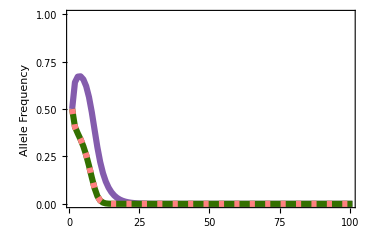

```mathematica
NoDelayLoop;
NoDelSingle50=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqA[3]},FrameLabel->{None," Allele Frequency"},
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[RGBColor[.4,.2,.6,.8], Thickness[.012]],Directive[RGBColor[.2,.44,.0,1.], Thickness[.012]],Directive[Pink,  Thickness[.012],Dashing[{0.01,0.02}]]},FrameStyle->Directive[20,Black],ImageSize->{370,Automatic}]
```

## 2-Geno release

### Sp=0.5

```mathematica
Nloci=3;
NGenotypes=3^Nloci;
NHaplotypes=2^Nloci;
recrate[1]=0.5; 
recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
h1=.95;

Generations=100;

thresh=10;

sc=0.05;
sp=0.5;

IntroFreq1=0.45;
IntroFreq2=0.05;

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
```

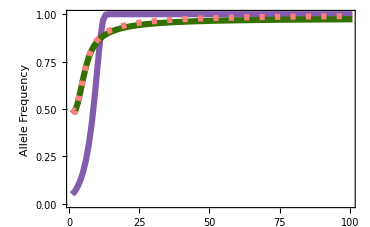

```mathematica
TwoGenoLoop;
TwoGeno50=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqA[3]},FrameLabel->{None," Allele Frequency",Null},
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[RGBColor[.4,.2,.6,.8], Thickness[.012]],Directive[RGBColor[.2,.44,.0,1.], Thickness[.012]],Directive[Pink,  Thickness[.012],Dashing[{0.01,0.02}]]},FrameStyle->Directive[20,Black],ImageSize->{370,Automatic}]
```

## 10 Gen delay

### Sp=0.5

```mathematica
Nloci=3;
NGenotypes=3^Nloci;
NHaplotypes=2^Nloci;
recrate[1]=0.5; 
recrate[2]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)
h1=.95;

Generations=100;

thresh=10;

sc=0.05;
sp=0.5;

IntroFreq1=0.5;
IntroFreq2=0.05;

GenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
GenoFreqA[[1,1]]=1;
```

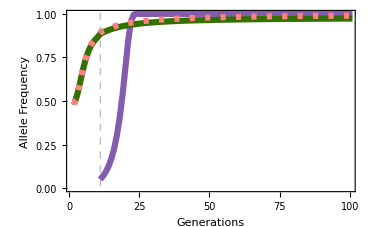

```mathematica
DelayLoop;
Delay50=ListPlot[{AlleleFreqA[1],AlleleFreqA[2],AlleleFreqA[3]},FrameLabel->{"Generations"," Allele Frequency"},
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,False,False},PlotStyle->{Directive[RGBColor[.4,.2,.6,.8], Thickness[.012]],Directive[RGBColor[.2,.44,.0,1.], Thickness[.012]],Directive[Pink,  Thickness[.012],Dashing[{0.01,0.02}]]},FrameStyle->Directive[20,Black],ImageSize->{370,Automatic},GridLines->{{thresh+1}},GridLinesStyle->Directive[Gray,Thick,Dashed]]
```

## Combined plot

```mathematica
TheLegend=LineLegend[{Directive[RGBColor[.4,.2,.6,.8], Thickness[.012]],Directive[RGBColor[.2,.44,.0,1.], Thickness[.012]],Directive[Pink,  Thickness[.012],Dashing[{0.01,0.02}]]},{"Homing construct 
with Payload (allele C_t)","Underdominance construct 
with Cas9 (allele B_t)","Underdominance construct 
w/o Cas9 (allele A_t)"},LabelStyle->20];
```

```mathematica
TimeSeriesPlot=Grid[{
{Style["A",28,Black,FontFamily->"Helvetica",TextAlignment->Center],Null},
{Rotate[Style["Single release   ",25,Black,FontFamily->"Helvetica"],90 Degree],NoDelSingle50},
{},
{Style["B",28,Black,FontFamily->"Helvetica",TextAlignment->Center],Null},
{Rotate[Style[" Single 2-genotype  
release",25,Black,FontFamily->"Helvetica",TextAlignment->Center],90 Degree],TwoGeno50}, 
{},
{Style["C",28,Black,FontFamily->"Helvetica",TextAlignment->Center],Null},
{Rotate[Style["          2-stage delayed  
           release",25,Black,FontFamily->"Helvetica",TextAlignment->Center],90 Degree],Delay50},
{Null,TheLegend}},
ItemSize->Full,Alignment->{Left,Top},Frame->Thick,

Background->{None,None,{{{1,2},{1,2}}->GrayLevel[.93],{{6,8},{1,2}}->GrayLevel[.93]}},Dividers->{{},{-2->Thick}}]
```

A | 
Single release    | -Graphics-
 | 
B | 
 Single 2-genotype  
release | -Graphics-
 | 
C | 
          2-stage delayed  
           release | -Graphics-
 |